```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Fq4π  = ReadList["plot4pi.txt", {Number,Number}];
Fqωπ = ReadList["omega.txt", {Number,Number}];
Fqinterf = ReadList["interf.txt", {Number,Number}]; 
picωπ=ListPlot[Fqωπ , Joined->True, PlotRange->All];
pic4π=ListPlot[Fq4π , Joined->True, PlotRange->All];
picinterf=ListPlot[Fqinterf , Joined->True, PlotRange->All];
picsum = ListPlot [100*Fqωπ+Fq4π, Joined -> True, PlotRange-> All];
a = {#[[1]],9*#[[2]]}&/@Fqωπ;
b= {0, #[[2]]}&/@Fq4π;
sum =a+b;
```

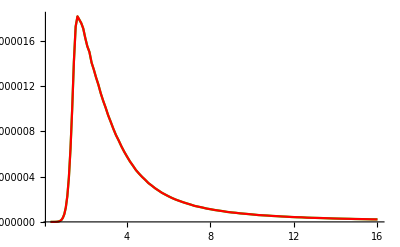

```mathematica
Show[ListPlot[Fqinterf , Joined->True, PlotRange->All, PlotStyle-> Green], ListPlot [sum, Joined -> True, PlotRange-> All, PlotStyle-> Red]]
```

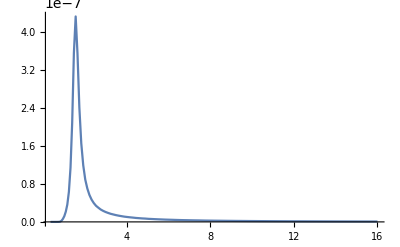

```mathematica
picωπ
```

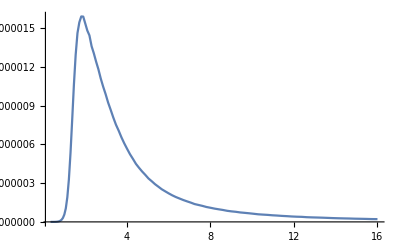

```mathematica
pic4π
```

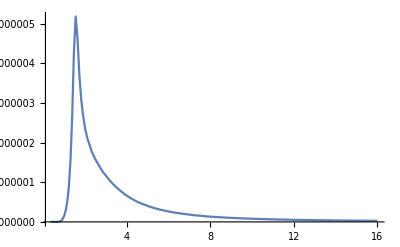

```mathematica
picinterf
```

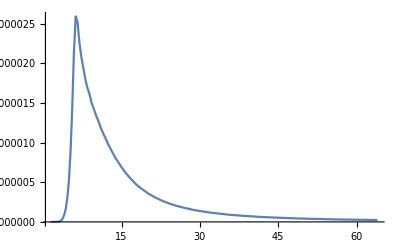

```mathematica
picsum
```